# Eigenvalue Distribution Images

I need to work out a good way to illustrate a sample of the eigenvalues of several thousand 100x100 matrices.  First think about illustrating the eigenvalues of a single matrix.

```mathematica
?Count
```

```mathematica
?Tally
```

{51,0,49}

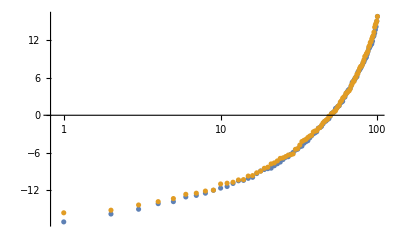

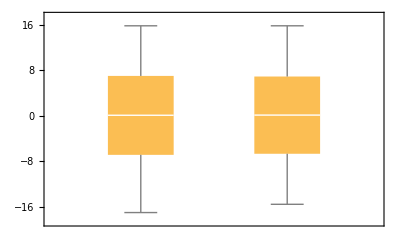

```mathematica
n=100;
A1=RandomReal[{-1,1},{n,n}];A1=A1+A1ᵀ;
λ1=Sort[Eigenvalues[A1]];
A2=RandomReal[{-1,1},{n,n}];A2=A2+A2ᵀ;
λ2=Sort[Eigenvalues[A2]];
(* Compute Index *)
Map[Count[Sign[λ],#]&,{-1,0,1}]
ListLogLinearPlot[{λ1,λ2}]
Histogram[λ1];
BoxWhiskerChart[{λ1,λ2},"Outliers"]
```

```mathematica
?BoxWhiskerChart
```